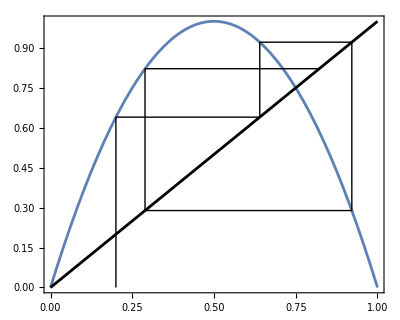

```mathematica
f[x_]:=4x(1-x);
g[{{a_,b_},{c_,d_},{e_,m_}}]:={{e,m},{m,f[m]},{f[m],f[m]}};
range={x,0,1};
n=3;
x0=0.2;
data=NestList[g,{{x0,0},{x0,f[x0]},{f[x0],f[x0]}},n];
Show[Plot[f[x],range],Plot[x,range,PlotStyle->Black],Graphics[Line/@data],AspectRatio->0.8,PlotRange->All,Frame->True]
```

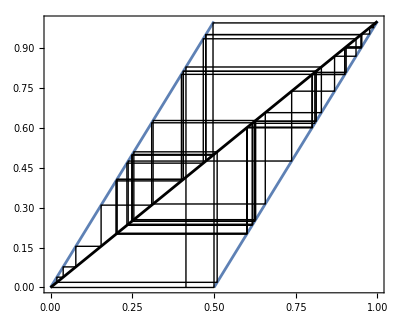

```mathematica
f[x_]:=Piecewise[{{2x,0<=x<1/2},{2x-1,1/2<=x<=1}}]
g[{{a_,b_},{c_,d_},{e_,m_}}]:={{e,m},{m,f[m]},{f[m],f[m]}};
range={x,0,1};
n=90;
x0=√2-1//N;
data=NestList[g,{{x0,0},{x0,f[x0]},{f[x0],f[x0]}},n];
Show[Plot[f[x],range],Plot[x,range,PlotStyle->Black],Graphics[Line/@data],AspectRatio->0.8,PlotRange->All,Frame->True]
```

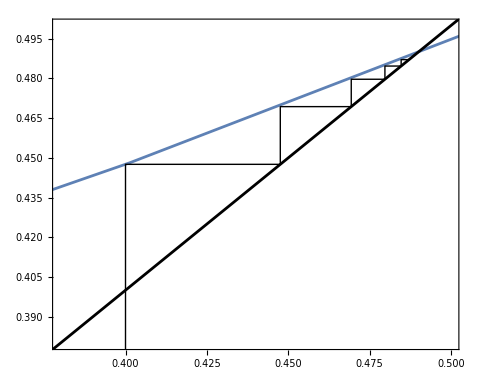

```mathematica
pref[x_]:=0.3 E^x;
f[x_]:=pref[x];
g[{{a_,b_},{c_,d_},{e_,m_}}]:={{e,m},{m,f[m]},{f[m],f[m]}};
range={x,0,5};
newrange={0.38,0.5};
n=4;
x0=0.4;
data=NestList[g,{{x0,0},{x0,f[x0]},{f[x0],f[x0]}},n];
Show[Plot[f[x],range],Plot[x,range,PlotStyle->Black],Graphics[Line/@data],AspectRatio->0.8,Frame->True,PlotRange->{newrange,newrange}]
```

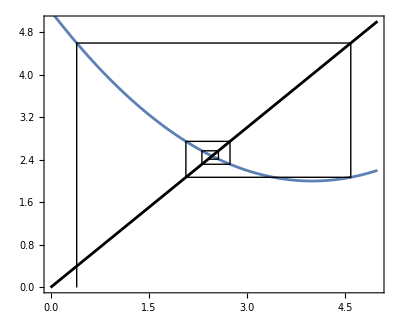

```mathematica
pref[x_]:=0.2 x^2+2;
f[x_]:=pref[x-4];
g[{{a_,b_},{c_,d_},{e_,m_}}]:={{e,m},{m,f[m]},{f[m],f[m]}};
range={x,0,5};
newrange={0,5};
n=5;
x0=0.4;
data=NestList[g,{{x0,0},{x0,f[x0]},{f[x0],f[x0]}},n];
Show[Plot[f[x],range],Plot[x,range,PlotStyle->Black],Graphics[Line/@data],AspectRatio->0.8,Frame->True,PlotRange->{newrange,newrange}]
```

```mathematica
Manipulate[Show[Plot[{x,x+μ+x^2},{x,-2,2}],PlotRange->{{-2,2},{-2,2}},Frame->True,AspectRatio->0.8],{μ,-2,2}]
```

```mathematica
ff[x_,μ_]:=-(1+μ)x+x^3;
Series[ff[ff[x,μ],μ],{x,0,3}]//Simplify
```

(1+μ)^2 x+(-1-μ-(1+μ)^3) x^3+O[x]^4

```mathematica
Solve[(1+μ)^2 x+(-1-μ-(1+μ)^3) x^3==x,x]//Simplify
```

{{x→0},{x→-(ⅈ √μ √(2+μ))/(√(-2-4 μ-3 μ^2-μ^3))},{x→(ⅈ √μ √(2+μ))/(√(-2-4 μ-3 μ^2-μ^3))}}

```mathematica
-2-4 μ-3 μ^2-μ^3//Simplify
```

-2-4 μ-3 μ^2-μ^3

```mathematica
(1+μ)+(1+μ)^3//Expand
```

2+4 μ+3 μ^2+μ^3